# Analytic Properties of 2PI Approximation Schemes

Author: Michael Brown
Supplement to thesis Chapter 2
Mathematica notebook to compute solution of the zero dimensional toy model and compare perturbation theory, Pade, Borel-Pade, 2PI and hybrid 2PI-Pade approximations.

## Classical action and solutions

```mathematica
Scl=1/2 m^2 q^2+1/(4!)λ q^4;
```

The classical solutions extremize the action:

```mathematica
clsoln=Solve[D[Scl,q]==0,q]
```

{{q→0},{q→-(ⅈ √6 m)/(√λ)},{q→(ⅈ √6 m)/(√λ)}}

The real solution is a minimum and the imaginary solutions are saddle points:

```mathematica
D[Scl,q,q]/.clsoln
```

{m^2,-2 m^2,-2 m^2}

with action:

```mathematica
Scl/.clsoln
```

{0,-(3 m^4)/(2 λ),-(3 m^4)/(2 λ)}

```mathematica
ContourPlot[Abs[Exp[-Scl]]/.{m->1,λ->1,q->x+ⅈ y},{x,-3,3},{y,-4,4},PlotPoints->30,Contours->Table[0.5 i,{i,20}],PlotRange->{0,10},FrameLabel->{"Re[q]","Im[q]"},PlotTheme->"Scientific",PlotLegends->Automatic,ContourShading->Automatic,ContourStyle->{Black,Dashed},LabelStyle->Medium]
ContourPlot[Arg[Exp[-Scl]]/.{m->1,λ->1,q->x+ⅈ y},{x,-3,3},{y,-4,4},PlotPoints->30,FrameLabel->{"Re[q]","Im[q]"},Contours->5,PlotTheme->"Scientific",PlotLegends->Automatic,ContourShading->Automatic,ContourStyle->{Black,Dashed},LabelStyle->Medium]
```

-Graphics-

-Graphics-

```mathematica
(*Export["z-integrand-abs.pdf",%93]
Export["z-integrand-arg.pdf",%94]*)
```

## Partition function and connected generating function

```mathematica
ClearAll[normalization,z,w]
```

```mathematica
normalization=Integrate[Exp[-Scl],{q,-∞,∞},Assumptions->{m>0,λ>0}]
```

(√3 m ⅇ^((3 m^4)/(4 λ)) 1/4(3 m^4)/(4 λ))/(√λ)

```mathematica
z[k_,l_]:=z[k,l]=1/normalization Integrate[Exp[-Scl-1/2 k q^2-1/(4!)l q^4],{q,-∞,∞},Assumptions->{λ+l>0,m^2+k>0}]
```

```mathematica
z[k,0]
```

(ⅇ^((3 (k+m^2)^2)/(4 λ)-(3 m^4)/(4 λ)) √(λ (k+m^2)) 1/4(3 (m^2+k)^2)/(4 λ))/(√λ m 1/4(3 m^4)/(4 λ))

```mathematica
w[k_,l_]:=w[k,l]=-Log[z[k,l]]
```

```mathematica
w[k,l]//FullSimplify[#,Assumptions->{λ+l>0,m^2+k>0}]&
```

-log((ⅇ^(3/4 (((k+m^2)^2)/(λ+l)-m^4/λ)) √((λ (k+m^2))/(λ+l)) 1/4(3 (m^2+k)^2)/(4 (l+λ)))/(m 1/4(3 m^4)/(4 λ)))

## Exact Propagator

```mathematica
Gexact=FullSimplify[2D[w[k,0],k]/.k->0]
```

(3 m^2 ((3/4(3 m^4)/(4 λ))/(1/4(3 m^4)/(4 λ))-1))/λ

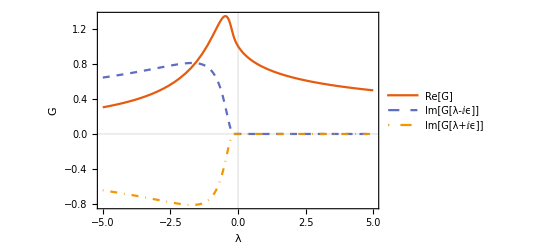

```mathematica
Plot[{Re[Gexact],Im[Gexact]/.λ->λ-0.00001ⅈ,Im[Gexact]/.λ->λ+0.00001ⅈ}/.m->1//Evaluate,{λ,-5,5},PlotLegends->{"Re[Ḡ]","Im[Ḡ[λ-ⅈϵ]]","Im[Ḡ[λ+ⅈϵ]]"},FrameLabel->{λ,Ḡ},PlotTheme->"Scientific",PlotStyle->{Dashing[{}],Dashed,DotDashed},LabelStyle->Medium]
```

```mathematica
(*Export["Gexact.pdf",%97]*)
```

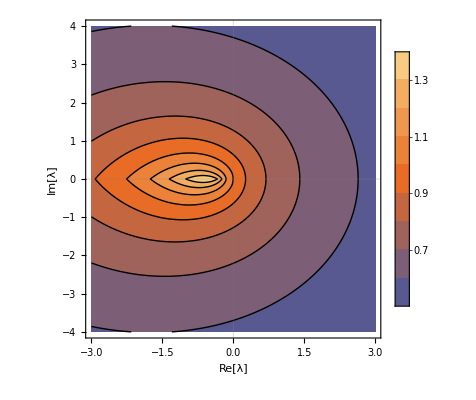

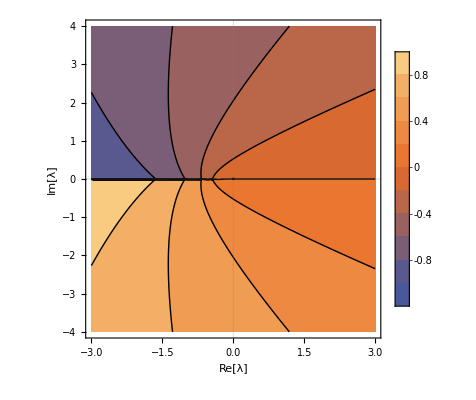

```mathematica
ContourPlot[Abs[Gexact]/.{m->1,λ->x+ⅈ y},{x,-3,3},{y,-4,4},PlotPoints->50,PlotRange->{0,10},FrameLabel->{"Re[λ]","Im[λ]"},PlotTheme->"Scientific",PlotLegends->Automatic,Contours->Table[i,{i,0,1.3,1/10}],LabelStyle->Medium]
ContourPlot[Arg[Gexact]/.{m->1,λ->x+ⅈ y},{x,-3,3},{y,-4,4},PlotPoints->40,FrameLabel->{"Re[λ]","Im[λ]"},PlotTheme->"Scientific",PlotLegends->Automatic,LabelStyle->Medium]
```

```mathematica
(*Export["Gexact-abs.pdf",%99]
Export["Gexact-arg.pdf",%100]*)
```

Discontinuity of the cut in λ:

```mathematica
disc=Series[(Gexact/.λ->λ+ⅈ ϵ)-(Gexact/.λ->λ-ⅈ ϵ),{ϵ,0,0},Assumptions->{m>0,λ<0,ϵ>0}]//Normal//FullSimplify[#,Assumptions->{m>0,λ<0,ϵ>0}]&
```

-(8 √2)/(π m^2 ((-1/4(3 m^4)/(4 λ))^2-(1/4(3 m^4)/(4 λ))^2))

Spectral function:

```mathematica
σexact=(Im[disc]/.λ->-λ)/(-2π)HeavisideTheta[λ]
```

(4 √2 λ Im(1/(m^2 ((-1/4-(3 m^4)/(4 λ))^2-(1/4-(3 m^4)/(4 λ))^2))))/π^2

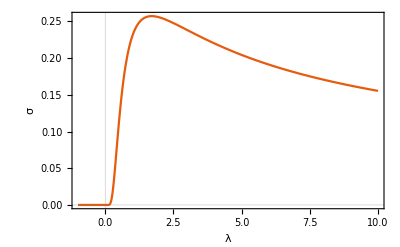

```mathematica
Plot[σexact/.m->1,{λ,-1,10},FrameLabel->{λ,σ},PlotTheme->"Scientific",LabelStyle->Medium]
```

```mathematica
(*Export["sigma-exact.pdf",%103]*)
```

## Exact Vertex Function

```mathematica
V4exact=Simplify[-(-4D[w[k,0],k,k]-2 Gexact^2)/Gexact^4/.k->0,Assumptions->{m>0,λ>0}];
```

```mathematica
Series[V4exact,{λ,0,2}]
```

λ-(3 λ^2)/(2 m^4)+O[λ]^(5/2)

## Perturbation series

```mathematica
ClearAll[Gpert]
```

```mathematica
Gpert[n_]:=Gpert[n]=Series[Gexact,{λ,0,n},Assumptions->{m>0,λ>0}]//Normal
```

```mathematica
Series[Gexact,{λ,0,1},Assumptions->{m>0,λ>0}]
```

1/m^2-λ/(2 m^6)+O(λ^(3/2))

```mathematica
Gpert[2]
```

(2 λ^2)/(3 m^10)-λ/(2 m^6)+1/m^2

```mathematica
Table[{n,Gpert[n]},{n,20}];Gpert[20]
```

(38131059969414309154 λ^20)/(59049 m^82)-(249615310568664912892639 λ^19)/(5159780352 m^78)+(75079607548893602 λ^18)/(19683 m^74)-(45494616421387671961 λ^17)/(143327232 m^70)+(20384334558514 λ^16)/(729 m^66)-(6944870083473751 λ^15)/(2654208 m^62)+(63444074282 λ^14)/(243 m^58)-(41657327595361 λ^13)/(1492992 m^54)+(2339780194 λ^12)/(729 m^50)-(33152545703 λ^11)/(82944 m^46)+(4394374 λ^10)/(81 m^42)-(18639247 λ^9)/(2304 m^38)+(108386 λ^8)/(81 m^34)-(858437 λ^7)/(3456 m^30)+(1418 λ^6)/(27 m^26)-(619 λ^5)/(48 m^22)+(34 λ^4)/(9 m^18)-(11 λ^3)/(8 m^14)+(2 λ^2)/(3 m^10)-λ/(2 m^6)+1/m^2

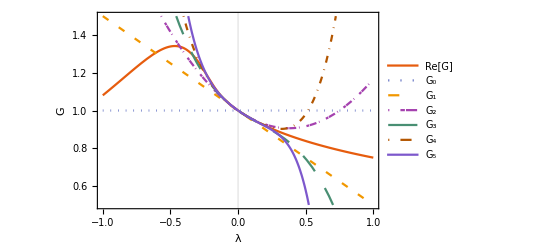

```mathematica
Plot[{Re[Gexact],Table[Gpert[n],{n,0,5}]}/.m->1//Evaluate,{λ,-1,1},PlotLegends->({"Re[Ḡ]",Table[Subscript[G, n],{n,0,5}]}//Flatten),FrameLabel->{λ,G},PlotTheme->"Scientific",PlotRange->{1/2,3/2},PlotStyle->({Automatic,Dotted,Dashing[{Small,Medium}],Dashing[{0,Small,Tiny}],Dashing[Large],DotDashed}),LabelStyle->Medium]
```

```mathematica
(*Export["G-pert-series.pdf",%105]*)
```

Relative error shows that the series is asymptotic, not convergent:

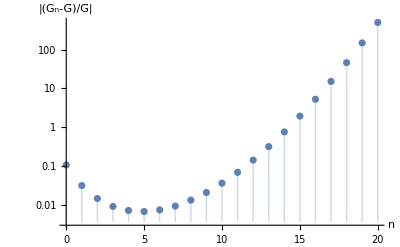

```mathematica
ListLogPlot[Table[{n,Abs[Gpert[n]/Gexact-1/.{m->1,λ->1/4}]},{n,0,20}]//N,Filling->Bottom,PlotRange->All,AxesLabel->{"n","|(G_n-Ḡ)/Ḡ|"},LabelStyle->Medium]
```

```mathematica
(*Export["G-pert-asympt-series.pdf",%107]*)
```

## Pade Approximants

```mathematica
Pade[n_]:=Pade[n]=PadeApproximant[Gexact,{λ,0,{n,n+1}}]
```

```mathematica
Table[{n,Pade[n]},{n,0,4}]//TableForm
```

0 | 1/(m^2 (λ/(2 m^4)+1))
1 | ((2 λ)/m^6+1/m^2)/((7 λ^2)/(12 m^8)+(5 λ)/(2 m^4)+1)
2 | ((59 λ^2)/(12 m^10)+(16 λ)/(3 m^6)+1/m^2)/((77 λ^3)/(72 m^12)+(43 λ^2)/(6 m^8)+(35 λ)/(6 m^4)+1)
3 | ((15 λ^3)/m^14+(155 λ^2)/(6 m^10)+(10 λ)/m^6+1/m^2)/((385 λ^4)/(144 m^16)+(295 λ^3)/(12 m^12)+(365 λ^2)/(12 m^8)+(21 λ)/(2 m^4)+1)
4 | ((7945 λ^4)/(144 m^18)+(1190 λ^3)/(9 m^14)+(315 λ^2)/(4 m^10)+(16 λ)/m^6+1/m^2)/((7315 λ^5)/(864 m^20)+(14315 λ^4)/(144 m^16)+(11935 λ^3)/(72 m^12)+(259 λ^2)/(3 m^8)+(33 λ)/(2 m^4)+1)

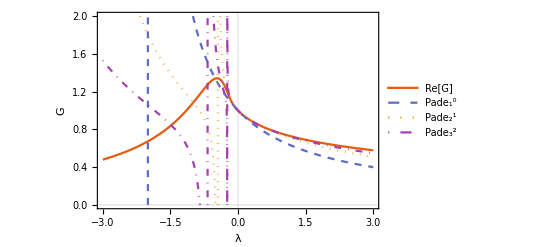

```mathematica
Plot[{Re[Gexact],Table[Pade[n],{n,0,2}]}/.m->1//Evaluate,{λ,-3,3},PlotLegends->({"Re[Ḡ]",Table[Subsuperscript[Pade,n+1,n],{n,0,2}]}//Flatten),FrameLabel->{λ,G},PlotTheme->"Scientific",PlotRange->{0,2},PlotStyle->{Automatic,Dashed,Dotted,DotDashed},LabelStyle->Medium]
```

```mathematica
(*Export["Pade-approx.pdf",%109]*)
```

Pade-approx.pdf

```mathematica
discPade[n_,ϵ_]:=(Pade[n]/.λ->λ+ⅈ ϵ)-(Pade[n]/.λ->λ-ⅈ ϵ)//FullSimplify[#,Assumptions->{m>0,λ<0,ϵ>0}]&
```

```mathematica
discPade[0,ϵ]
```

-(4 ⅈ m^2 ϵ)/((λ+2 m^4)^2+ϵ^2)

Spectral function:

```mathematica
σPade[n_,ϵ_]:=σPade[n,ϵ]=(Im[discPade[n,ϵ]]/.λ->-λ)/(-2π)HeavisideTheta[λ]
```

```mathematica
σPade[0,0.0001]/.m->1
```

-(λ Im(-(0.+0.0001 ⅈ)/(0.25 λ^2-1. λ+1.)))/(2 π)

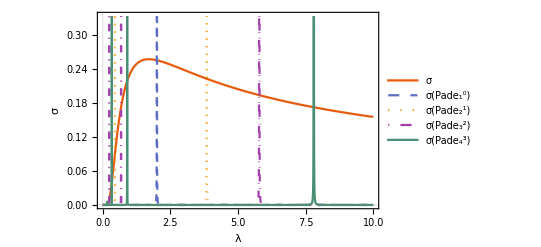

```mathematica
Plot[{σexact,Table[σPade[n,0.00001],{n,0,3}]}/.m->1//Evaluate,{λ,0,10},FrameLabel->{λ,σ},PlotTheme->"Scientific",PlotLegends->({"σ",Table[σ[Subsuperscript[Pade,n+1,n]],{n,0,3}]}//Flatten),PlotRange->{0,1/3},PlotStyle->{Automatic,Dashed,Dotted,DotDashed},PlotPoints->100,LabelStyle->Medium]
```

```mathematica
(*Export["sigma-Pade.pdf",%111]*)
```

sigma-Pade.pdf

## Borel Pade

```mathematica
ClearAll[BorelSeriesCoeff,BorelPade,BorelTransf]
```

```mathematica
BorelSeriesCoeff[n_]:=BorelSeriesCoeff[n]=(SeriesCoefficient[Gexact,{λ,0,n},Assumptions->{m>0,λ>0}] 1/(n!))
```

```mathematica
BorelTransf[n_]:=BorelTransf[n]=Sum[BorelSeriesCoeff[k] λ^k x^k,{k,0,n}]
```

```mathematica
BorelPade[a_,b_]:=BorelPade[a,b]=PadeApproximant[BorelTransf[a+b],{x,0,{a,b}}]
```

```mathematica
Table[BorelPade[a,b],{a,3},{b,3}]//Simplify
```

((6 m^4+x λ)/(6 m^6+4 x λ m^2) | (6 m^2 (4 m^4+x λ))/(24 m^8+18 x λ m^4+x^2 λ^2) | (48 m^6 (9 m^4+2 x λ))/(432 m^12+312 x λ m^8+12 x^2 λ^2 m^4+x^3 λ^3)
(96 m^8+18 x λ m^4-x^2 λ^2)/(96 m^10+66 x λ m^6) | (72 m^8+12 x λ m^4-x^2 λ^2)/(72 m^10+48 x λ m^6-x^2 λ^2 m^2) | (m^2 (360 m^8+468 x λ m^4+97 x^2 λ^2))/(360 m^12+648 x λ m^8+301 x^2 λ^2 m^4+17 x^3 λ^3)
(4752 m^12+888 x λ m^8-48 x^2 λ^2 m^4-x^3 λ^3)/(4752 m^14+3264 x λ m^10) | (360 m^12+1692 x λ m^8+301 x^2 λ^2 m^4-17 x^3 λ^3)/(m^6 (360 m^8+1872 x λ m^4+1117 x^2 λ^2)) | (6120 m^12+5220 x λ m^8+1193 x^2 λ^2 m^4+38 x^3 λ^3)/(6120 m^14+8280 x λ m^10+3293 x^2 λ^2 m^6+327 x^3 λ^3 m^2))

```mathematica
BPG[a_,b_]:=BPG[a,b]=LaplaceTransform[BorelPade[a,b],x,s]/.s->1//Simplify//FullSimplify[#,Assumptions->{λ>0,m>0}]&
```

```mathematica
Table[BPG[a,1],{a,0,3}]
```

{(2 m^2 ⅇ^((2 m^4)/λ) 0(2 m^4)/λ)/λ,(2-(9 m^4 ⅇ^((3 m^4)/(2 λ)) -(3 m^4)/(2 λ))/λ)/(8 m^2),(-(8192 m^8 ⅇ^((16 m^4)/(11 λ)) -(16 m^4)/(11 λ))/λ-121 λ+2354 m^4)/(7986 m^6),-(1056655611 m^12 ⅇ^((99 m^4)/(68 λ)) -(99 m^4)/(68 λ)+68 λ (9248 λ^2-4419447 m^8+215220 λ m^4))/(1026306048 λ m^10)}

```mathematica
ClearAll[NBPG,NPGs]
```

```mathematica
NBPG[a_,b_]:=NBPG[a,b]=Table[{λ,LaplaceTransform[BorelPade[a,b],x,s]/.s->1/.m->1},{λ,0,5,0.1}]
```

```mathematica
(*NBPG[1,1]=Table[{λ,NIntegrate[Exp[-x]BorelPade[1,2]/.m->1,{x,0,∞},WorkingPrecision->30]},{λ,0,5,0.1}];*)
NBPG[2,1]=Table[{λ,NIntegrate[Exp[-x]BorelPade[2,2]/.m->1,{x,0,∞},WorkingPrecision->45]},{λ,0,5,0.1}];
NBPG[3,1]=Table[{λ,NIntegrate[Exp[-x]BorelPade[3,2]/.m->1,{x,0,∞},WorkingPrecision->30]},{λ,0,5,0.1}];
NBPG[1,2]=Table[{λ,NIntegrate[Exp[-x]BorelPade[1,2]/.m->1,{x,0,∞},WorkingPrecision->30]},{λ,0,5,0.1}];
NBPG[2,2]=Table[{λ,NIntegrate[Exp[-x]BorelPade[2,2]/.m->1,{x,0,∞},WorkingPrecision->45]},{λ,0,5,0.1}];
NBPG[3,2]=Table[{λ,NIntegrate[Exp[-x]BorelPade[3,2]/.m->1,{x,0,∞},WorkingPrecision->30]},{λ,0,5,0.1}];
NBPG[1,3]=Table[{λ,NIntegrate[Exp[-x]BorelPade[1,3]/.m->1,{x,0,∞},WorkingPrecision->30]},{λ,0,5,0.1}];
NBPG[2,3]=Table[{λ,NIntegrate[Exp[-x]BorelPade[2,3]/.m->1,{x,0,∞},WorkingPrecision->30]},{λ,0,5,0.1}];
NBPG[3,3]=Table[{λ,NIntegrate[Exp[-x]BorelPade[3,3]/.m->1,{x,0,∞},WorkingPrecision->30]},{λ,0,5,0.1}];
```

NIntegrate::precw: The precision of the argument function (TraditionalForm`1.\ ⅇ^-x) is less than WorkingPrecision (TraditionalForm`44.99999999999999`).

NIntegrate::precw: The precision of the argument function (TraditionalForm`ⅇ^-x\ (1 + 0.0166667\ x - 0.000138889\ x^2)/1 + 0.0666667\ x - 0.000138889\ x^2) is less than WorkingPrecision (TraditionalForm`44.99999999999999`).

NIntegrate::precw: The precision of the argument function (TraditionalForm`ⅇ^-x\ (1 + 0.0333333\ x - 0.000555556\ x^2)/1 + 0.133333\ x - 0.000555556\ x^2) is less than WorkingPrecision (TraditionalForm`44.99999999999999`).

General::stop: Further output of NIntegrate :: precw will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after TraditionalForm`9 recursive bisections in TraditionalForm`x near TraditionalForm`{x} = TraditionalForm`{75.1489285231439676997156244380075988512619334}. NIntegrate obtained TraditionalForm`0.817350542166047517630099509788974127068805045`45. and TraditionalForm`5.29042104300005053711421868277289770970563316`45.*^-33 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after TraditionalForm`9 recursive bisections in TraditionalForm`x near TraditionalForm`{x} = TraditionalForm`{68.0079526086468872620272154053242968119309705}. NIntegrate obtained TraditionalForm`0.798202524039832931984313148207195779211279388`45. and TraditionalForm`9.44027351128877318557846137330198559451747553`45.*^-29 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after TraditionalForm`9 recursive bisections in TraditionalForm`x near TraditionalForm`{x} = TraditionalForm`{56.8807320667301246894755751938663576579826771}. NIntegrate obtained TraditionalForm`0.780690780772040543747074919531026963953427732`45. and TraditionalForm`1.61918011095201769088758421592912547028083897`45.*^-24 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::precw: The precision of the argument function (TraditionalForm`1.\ ⅇ^-x) is less than WorkingPrecision (TraditionalForm`30.`).

NIntegrate::precw: The precision of the argument function (TraditionalForm`ⅇ^-x\ (1 + 0.47\ x + 0.00836111\ x^2 - 0.0000472222\ x^3)/1 + 0.52\ x + 0.0310278\ x^2) is less than WorkingPrecision (TraditionalForm`30.`).

NIntegrate::precw: The precision of the argument function (TraditionalForm`ⅇ^-x\ (1 + 0.94\ x + 0.0334444\ x^2 - 0.000377778\ x^3)/1 + 1.04\ x + 0.124111\ x^2) is less than WorkingPrecision (TraditionalForm`30.`).

General::stop: Further output of NIntegrate :: precw will be suppressed during this calculation.

NIntegrate::precw: The precision of the argument function (TraditionalForm`1.\ ⅇ^-x) is less than WorkingPrecision (TraditionalForm`30.`).

NIntegrate::precw: The precision of the argument function (TraditionalForm`ⅇ^-x\ (1 + 0.025\ x)/1 + 0.075\ x + 0.000416667\ x^2) is less than WorkingPrecision (TraditionalForm`30.`).

NIntegrate::precw: The precision of the argument function (TraditionalForm`ⅇ^-x\ (1 + 0.05\ x)/1 + 0.15\ x + 0.00166667\ x^2) is less than WorkingPrecision (TraditionalForm`30.`).

General::stop: Further output of NIntegrate :: precw will be suppressed during this calculation.

NIntegrate::precw: The precision of the argument function (TraditionalForm`1.\ ⅇ^-x) is less than WorkingPrecision (TraditionalForm`44.99999999999999`).

NIntegrate::precw: The precision of the argument function (TraditionalForm`ⅇ^-x\ (1 + 0.0166667\ x - 0.000138889\ x^2)/1 + 0.0666667\ x - 0.000138889\ x^2) is less than WorkingPrecision (TraditionalForm`44.99999999999999`).

NIntegrate::precw: The precision of the argument function (TraditionalForm`ⅇ^-x\ (1 + 0.0333333\ x - 0.000555556\ x^2)/1 + 0.133333\ x - 0.000555556\ x^2) is less than WorkingPrecision (TraditionalForm`44.99999999999999`).

General::stop: Further output of NIntegrate :: precw will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after TraditionalForm`9 recursive bisections in TraditionalForm`x near TraditionalForm`{x} = TraditionalForm`{75.1489285231439676997156244380075988512619334}. NIntegrate obtained TraditionalForm`0.817350542166047517630099509788974127068805045`45. and TraditionalForm`5.29042104300005053711421868277289770970563316`45.*^-33 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after TraditionalForm`9 recursive bisections in TraditionalForm`x near TraditionalForm`{x} = TraditionalForm`{68.0079526086468872620272154053242968119309705}. NIntegrate obtained TraditionalForm`0.798202524039832931984313148207195779211279388`45. and TraditionalForm`9.44027351128877318557846137330198559451747553`45.*^-29 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after TraditionalForm`9 recursive bisections in TraditionalForm`x near TraditionalForm`{x} = TraditionalForm`{56.8807320667301246894755751938663576579826771}. NIntegrate obtained TraditionalForm`0.780690780772040543747074919531026963953427732`45. and TraditionalForm`1.61918011095201769088758421592912547028083897`45.*^-24 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::precw: The precision of the argument function (TraditionalForm`1.\ ⅇ^-x) is less than WorkingPrecision (TraditionalForm`30.`).

NIntegrate::precw: The precision of the argument function (TraditionalForm`ⅇ^-x\ (1 + 0.47\ x + 0.00836111\ x^2 - 0.0000472222\ x^3)/1 + 0.52\ x + 0.0310278\ x^2) is less than WorkingPrecision (TraditionalForm`30.`).

NIntegrate::precw: The precision of the argument function (TraditionalForm`ⅇ^-x\ (1 + 0.94\ x + 0.0334444\ x^2 - 0.000377778\ x^3)/1 + 1.04\ x + 0.124111\ x^2) is less than WorkingPrecision (TraditionalForm`30.`).

General::stop: Further output of NIntegrate :: precw will be suppressed during this calculation.

NIntegrate::precw: The precision of the argument function (TraditionalForm`1.\ ⅇ^-x) is less than WorkingPrecision (TraditionalForm`30.`).

NIntegrate::precw: The precision of the argument function (TraditionalForm`ⅇ^-x\ (1 + 0.0222222\ x)/1 + 0.0722222\ x + 0.000277778\ x^2 + 2.31481×10^-6\ x^3) is less than WorkingPrecision (TraditionalForm`30.`).

NIntegrate::precw: The precision of the argument function (TraditionalForm`ⅇ^-x\ (1 + 0.0444444\ x)/1 + 0.144444\ x + 0.00111111\ x^2 + 0.0000185185\ x^3) is less than WorkingPrecision (TraditionalForm`30.`).

General::stop: Further output of NIntegrate :: precw will be suppressed during this calculation.

NIntegrate::precw: The precision of the argument function (TraditionalForm`1.\ ⅇ^-x) is less than WorkingPrecision (TraditionalForm`30.`).

NIntegrate::precw: The precision of the argument function (TraditionalForm`ⅇ^-x\ (1 + 0.13\ x + 0.00269444\ x^2)/1 + 0.18\ x + 0.00836111\ x^2 + 0.0000472222\ x^3) is less than WorkingPrecision (TraditionalForm`30.`).

NIntegrate::precw: The precision of the argument function (TraditionalForm`ⅇ^-x\ (1 + 0.26\ x + 0.0107778\ x^2)/1 + 0.36\ x + 0.0334444\ x^2 + 0.000377778\ x^3) is less than WorkingPrecision (TraditionalForm`30.`).

General::stop: Further output of NIntegrate :: precw will be suppressed during this calculation.

NIntegrate::precw: The precision of the argument function (TraditionalForm`1.\ ⅇ^-x) is less than WorkingPrecision (TraditionalForm`30.`).

NIntegrate::precw: The precision of the argument function (TraditionalForm`ⅇ^-x\ (1 + 0.0852941\ x + 0.00194935\ x^2 + 6.20915×10^-6\ x^3)/1 + 0.135294\ x + 0.00538072\ x^2 + 0.0000534314\ x^3) is less than WorkingPrecision (TraditionalForm`30.`).

NIntegrate::precw: The precision of the argument function (TraditionalForm`ⅇ^-x\ (1 + 0.170588\ x + 0.00779739\ x^2 + 0.0000496732\ x^3)/1 + 0.270588\ x + 0.0215229\ x^2 + 0.000427451\ x^3) is less than WorkingPrecision (TraditionalForm`30.`).

General::stop: Further output of NIntegrate :: precw will be suppressed during this calculation.

```mathematica
(*Table[NBPG[a,b],{a,3},{b,3}]*)
```

```mathematica
NPGs=Table[{a,b,NBPG[a,b]},{a,3},{b,3}];
```

```mathematica
plotdata=({{#[[;;,1]],(#[[;;,2]])/Thread[Gexact/.m->1/.λ->#[[;;,1]]]}//Transpose}&/@Flatten[NPGs,1][[;;,3]])[[;;,1,;;,;;]];
```

Power::infy: Infinite expression TraditionalForm`1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

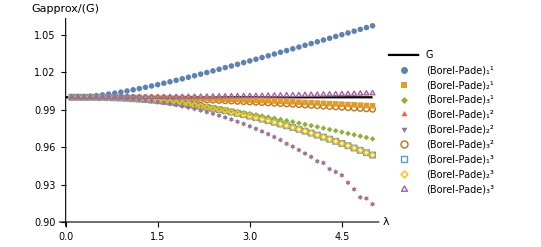

```mathematica
Show[Plot[1,{λ,0,5},PlotRange->{0.9,1.06},AxesLabel->{λ,"Gapprox/(Ḡ)"},PlotStyle->{Black,Thick},PlotLegends->{"Ḡ"}],ListPlot[plotdata,PlotLegends->({Subsuperscript["Borel-Pade",ToString[#[[2]]],ToString[#[[1]]]]&/@Flatten[NPGs,1][[;;,1;;2]]}//Flatten),PlotMarkers-> {Automatic,Medium}],LabelStyle->Medium]
```

```mathematica
(*Export["Gbar-PadeBorel.pdf",%132]*)
```

Gbar-PadeBorel.pdf

```mathematica
BPσs=Table[{a,b,InverseLaplaceTransform[BorelPade[a,b],x,v]/.v->1},{a,3},{b,3}]//FullSimplify[#,Assumptions->λ>0]&
```

({1,1,(9 ⅇ^(-(3 m^4)/(2 λ)) m^2)/(8 λ)} | {1,2,(√(3/19) ⅇ^(-((9+√57) m^4)/λ) (5+√57+(-5+√57) ⅇ^((2 √57 m^4)/λ)) m^2)/λ} | {1,3,(ⅈ m^2 (ⅇ^((m^4 Root[#1^3+12 #1^2+312 #1+432&,3])/λ) Root[#1^6-531216 #1^4+70547609664 #1^2+3718344077593344&,2]+ⅇ^((m^4 Root[#1^3+12 #1^2+312 #1+432&,1])/λ) Root[#1^6-531216 #1^4+70547609664 #1^2+3718344077593344&,3]+ⅇ^((m^4 Root[#1^3+12 #1^2+312 #1+432&,2])/λ) Root[#1^6-531216 #1^4+70547609664 #1^2+3718344077593344&,6]))/(√37491 λ)}
{2,1,(4096 ⅇ^(-(16 m^4)/(11 λ)) m^2)/(3993 λ)} | {2,2,(12 ⅇ^((24 m^4)/λ) m^2 (3 cosh((18 √2 m^4)/λ)+2 √2 sinh((18 √2 m^4)/λ)))/λ} | {2,3,-(m^2 (ⅇ^((m^4 Root[17 #1^3+301 #1^2+648 #1+360&,1])/λ) Root[#1^6-647602769169561600 #1^4+17406646562474287742756994416640000 #1^2-11535526384625628118042992967680000000000000000&,1]+ⅇ^((m^4 Root[17 #1^3+301 #1^2+648 #1+360&,2])/λ) Root[#1^6-647602769169561600 #1^4+17406646562474287742756994416640000 #1^2-11535526384625628118042992967680000000000000000&,2]+ⅇ^((m^4 Root[17 #1^3+301 #1^2+648 #1+360&,3])/λ) Root[#1^6-647602769169561600 #1^4+17406646562474287742756994416640000 #1^2-11535526384625628118042992967680000000000000000&,4]))/(73440 √5181902 λ)}
{3,1,(352218537 ⅇ^(-(99 m^4)/(68 λ)) m^2)/(342102016 λ)} | {3,2,(9 √(2/6583) ⅇ^(-(6 (156+√13166) m^4)/(1117 λ)) (4554518636+39693141 √13166+(-4554518636+39693141 √13166) ⅇ^((12 √13166 m^4)/(1117 λ))) m^2)/(1393668613 λ)} | {3,3,-(m^2 (ⅇ^((m^4 Root[327 #1^3+3293 #1^2+8280 #1+6120&,1])/λ) Root[106929 #1^6-5310598411456636003040 #1^4+73128468015928331145379022721408000000 #1^2-187227994595197834188856209234354554209766400000000000&,1]+ⅇ^((m^4 Root[327 #1^3+3293 #1^2+8280 #1+6120&,3])/λ) Root[106929 #1^6-5310598411456636003040 #1^4+73128468015928331145379022721408000000 #1^2-187227994595197834188856209234354554209766400000000000&,2]+ⅇ^((m^4 Root[327 #1^3+3293 #1^2+8280 #1+6120&,2])/λ) Root[106929 #1^6-5310598411456636003040 #1^4+73128468015928331145379022721408000000 #1^2-187227994595197834188856209234354554209766400000000000&,4]))/(1308 √5790084110 λ)})

```mathematica
Subsuperscript["Borel-Pade",ToString[#[[2]]],ToString[#[[1]]]]&/@Flatten[BPσs,1][[;;,1;;2]]
```

{(Borel-Pade)_1^1,(Borel-Pade)_2^1,(Borel-Pade)_3^1,(Borel-Pade)_1^2,(Borel-Pade)_2^2,(Borel-Pade)_3^2,(Borel-Pade)_1^3,(Borel-Pade)_2^3,(Borel-Pade)_3^3}

N::meprec: Internal precision limit $MaxExtraPrecision = TraditionalForm`50.` reached while evaluating TraditionalForm`39693141\ √13166.

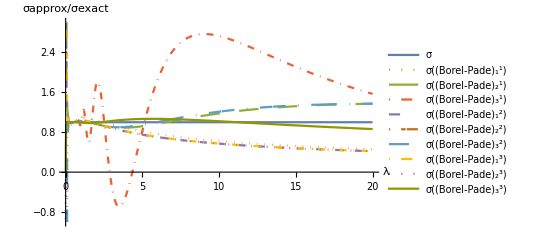

```mathematica
Plot[Re@{1,(Flatten[BPσs,1][[;;,3]])/σexact/.m->1}//Flatten//Evaluate,{λ,0,20},PlotLegends->({σ,σ[Subsuperscript["Borel-Pade",ToString[#[[2]]],ToString[#[[1]]]]]&/@Flatten[BPσs,1][[;;,1;;2]]}//Flatten),AxesLabel->{λ,"σapprox/σexact"},PlotRange->{-1,3},PlotStyle->({{Automatic,Thick},Dotted,Dashing[Large],DotDashed,Dashing[{Small,Medium}],Dashing[{0,Small,Tiny}],Dashing[{Medium,Medium,0}],DotDashed,{Dotted,Thick}}),LabelStyle->Medium]
```

```mathematica
(*Export["sigma-PadeBorel.pdf",%134]*)
```

sigma-PadeBorel.pdf

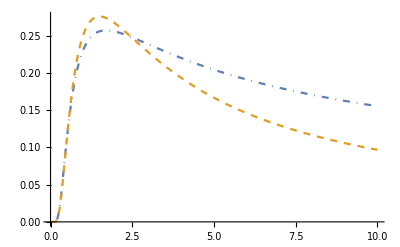

```mathematica
Plot[{σexact,(HeavisideTheta[λ]InverseLaplaceTransform[BorelPade[1,1],x,v]/.v->1)}/.m->1//Evaluate,{λ,0,10},PlotStyle->{DotDashed,Dashed}]
```

```mathematica
FindRoot[Re[BPG[0,1]]/.m->1,{λ,-5}]
```

{λ→-5.36902}

```mathematica
BPG[0,1]/.m->1/.{λ->-5.369020701641415}
```

4.02578×10^-17+0.806319 ⅈ

## 2 PI Approximations

```mathematica
Clear[Γ2,G]
```

```mathematica
Γ2[G_]:=Γ2[G]=1/2 Log[G^-1]+1/2 m^2 G+γ2[G]
```

To determine γ2[G] we expand the left and right hand sides of the G equation of motion to O(G^n):

```mathematica
GeomExpansion[n_]:=Module[{γ2=Sum[γ[i](λ G^2)^i,{i,1,n}]},
Series[{Gexact,1/(m^2+2D[γ2,G])/.G->Gexact},{λ,0,n}]//Normal]
```

and match coefficients:

```mathematica
nthMatchingEqs[n_]:=Thread[CoefficientList[GeomExpansion[n][[1]],λ]==CoefficientList[GeomExpansion[n][[2]],λ]]
```

```mathematica
GeomExpansion[3]
```

{-(11 λ^3)/(8 m^14)+(2 λ^2)/(3 m^10)-λ/(2 m^6)+1/m^2,-(4 (48 (γ(1))^3+12 (γ(1))^2-48 γ(2) γ(1)+2 γ(1)-9 γ(2)+9 γ(3)) λ^3)/(3 m^14)+(2 (8 (γ(1))^2+γ(1)-4 γ(2)) λ^2)/m^10-(4 γ(1) λ)/m^6+1/m^2}

```mathematica
γ2coeffs=Solve[nthMatchingEqs[20],Table[γ[i],{i,20}]][[1]];
```

```mathematica
Sum[γ[i](λ G^2)^i,{i,1,20}]/.γ2coeffs
```

-(1134464795789402074081 G^40 λ^20)/679477248+(70482935423952918475 G^38 λ^19)/537919488-(921138067678697395 G^36 λ^18)/84934656+(4231429245358235 G^34 λ^17)/4456448-(1665014342007385 G^32 λ^16)/18874368+(5148422676667 G^30 λ^15)/589824-(11440081763125 G^28 λ^14)/12386304+(201268707239 G^26 λ^13)/1916928-(3802117511 G^24 λ^12)/294912+(697775057 G^22 λ^11)/405504-(5151939 G^20 λ^10)/20480+(374755 G^18 λ^9)/9216-(271217 G^16 λ^8)/36864+(8143 G^14 λ^7)/5376-(93 G^12 λ^6)/256+(101 G^10 λ^5)/960-(5 G^8 λ^4)/128+(G^6 λ^3)/48-(G^4 λ^2)/48+(G^2 λ)/8

The series has super-exponential coefficients, aymptotically the same as perturbation theory up to a constant factor:

```mathematica
Table[{i,γ[i]/(.03(-2/3)^(i-1)(i-1)!)},{i,20}]/.γ2coeffs//TableForm//N
```

1. | 4.16667
2. | 1.04167
3. | 0.78125
4. | 0.732422
5. | 0.739746
6. | 0.766296
7. | 0.798765
8. | 0.831384
9. | 0.861575
10. | 0.888337
11. | 0.911483
12. | 0.931236
13. | 0.947998
14. | 0.962215
15. | 0.974316
16. | 0.984677
17. | 0.993614
18. | 1.00139
19. | 1.0082
20. | 1.01422

```mathematica
Clear[Gsolns]
```

```mathematica
Gsolns[n_]:=Gsolns[n]=G/.Solve[0==D[1/2 Log[G^-1]+1/2 m^2 G+Sum[γ[i](λ G^2)^i,{i,1,n}],G]/.γ2coeffs,G]//FullSimplify[#,Assumptions->{m>0,λ>0}]&
```

```mathematica
Gsolns[1]
```

{-(√(2 λ+m^4)+m^2)/λ,(√(2 λ+m^4)-m^2)/λ}

```mathematica
Gsolns[3]
```

{Root[3 #1^6 λ^3-2 #1^4 λ^2+6 #1^2 λ+12 #1 m^2-12&,1],Root[3 #1^6 λ^3-2 #1^4 λ^2+6 #1^2 λ+12 #1 m^2-12&,2],Root[3 #1^6 λ^3-2 #1^4 λ^2+6 #1^2 λ+12 #1 m^2-12&,3],Root[3 #1^6 λ^3-2 #1^4 λ^2+6 #1^2 λ+12 #1 m^2-12&,4],Root[3 #1^6 λ^3-2 #1^4 λ^2+6 #1^2 λ+12 #1 m^2-12&,5],Root[3 #1^6 λ^3-2 #1^4 λ^2+6 #1^2 λ+12 #1 m^2-12&,6]}

```mathematica
Series[Gsolns[1],{λ,0,1}]//FullSimplify[#,Assumptions->{m>0,λ>0}]&
```

{-(2 m^2)/λ-1/m^2+λ/(2 m^6)+O(λ^2),1/m^2-λ/(2 m^6)+O(λ^2)}

```mathematica
g2loop=Gsolns[1][[2]]
```

(√(2 λ+m^4)-m^2)/λ

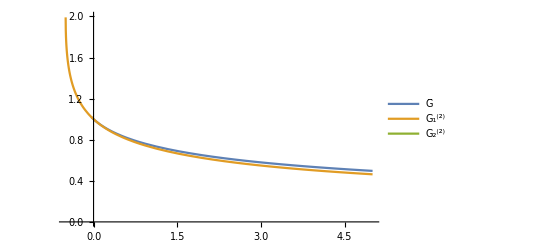

```mathematica
Plot[{Gexact,g2loop,Gsolns[2][[2]]}/.m->1//Evaluate,{λ,-5,5},PlotLegends->{Ḡ,Subsuperscript[G,1,"(2)"],Subsuperscript[G,2,"(2)"]},PlotRange->{0,2}]
```

```mathematica
Series[(Gsolns[2][[1]]/.λ->λ+ⅈ ϵ)-(Gsolns[2][[1]]/.λ->λ-ⅈ ϵ)/.m->1,{ϵ,0,0},Assumptions->{λ<-5}]
```

1/(2 λ)(√(-(-2 ⅈ √(50 λ^2-207 λ-81)+23 λ+18)^(1/3) Conjugate[(λ^(2/3))]-(9 Conjugate[(λ^(4/3))])/((-2 ⅈ √(50 λ^2-207 λ-81)+23 λ+18)^(1/3))-12/(√((-2 ⅈ √(50 λ^2-207 λ-81)+23 λ+18)^(1/3) Conjugate[(1/λ^(4/3))]+(9 Conjugate[(1/λ^(2/3))])/((-2 ⅈ √(50 λ^2-207 λ-81)+23 λ+18)^(1/3))+2/λ))+4 λ)+λ √((-2 ⅈ √(50 λ^2-207 λ-81)+23 λ+18)^(1/3) Conjugate[(1/λ^(4/3))]+9/((23 λ^3-2 ⅈ √(50 λ^2-207 λ-81) λ^2+18 λ^2)^(1/3))+2/λ)-√(9/((λ^2 (2 √(-50 λ^2+207 λ+81)+23 λ+18))^(1/3))+((2 √(-50 λ^2+207 λ+81)+23 λ+18)^(1/3))/λ^(4/3)+2/λ) λ-√(-(9 λ^(4/3))/((2 √(-50 λ^2+207 λ+81)+23 λ+18)^(1/3))-(2 √(-50 λ^2+207 λ+81)+23 λ+18)^(1/3) λ^(2/3)-12/(√(((2 √(-50 λ^2+207 λ+81)+23 λ+18)^(1/3))/λ^(4/3)+9/(λ^(2/3) (2 √(-50 λ^2+207 λ+81)+23 λ+18)^(1/3))+2/λ))+4 λ))+O(ϵ^1)

```mathematica
(-1/(2π ⅈ)Series[(g2loop/.λ->λ+ⅈ ϵ)-(g2loop/.λ->λ-ⅈ ϵ)/.m->1,{ϵ,0,0},Assumptions->{λ<-1/2}]//FullSimplify[#,Assumptions->{λ<-1/2}]&//Normal)/.λ->-λ
```

(√(2 λ-1))/(π λ)

```mathematica
σ2=(√(2λ-m^4))/(π λ)HeavisideTheta[λ-m^4/2]
```

(√(2 λ-m^4) λ-m^4/2)/(π λ)

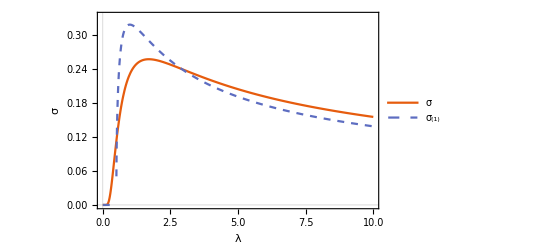

```mathematica
Plot[{σexact,σ2}/.m->1//Evaluate,{λ,0,10},FrameLabel->{λ,σ},PlotTheme->"Scientific",PlotLegends->{"σ","σ_(1)"},PlotRange->{0,1/3},PlotStyle->{Automatic,Dashed},PlotPoints->50,LabelStyle->Medium]
```

```mathematica
(*Export["sigma-2pi-2loop.pdf",%137]*)
```

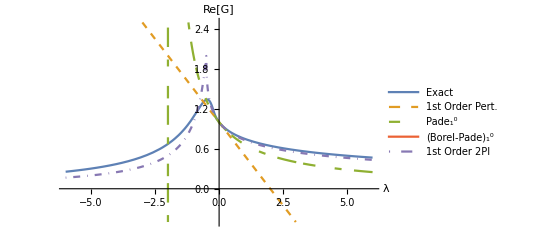

```mathematica
Plot[Re/@{Gexact,Gpert[1],PadeApproximant[Gpert[1],{λ,0,{0,1}}],BPG[0,1],g2loop}/.m->1//Evaluate,{λ,-6,6},PlotRange->{-.5,2.5},PlotLegends->{"Exact","1st Order Pert.",Subsuperscript["Pade",1,0],Subsuperscript["Borel-Pade",1,0],"1st Order 2PI"},AxesLabel->{λ,"Re[Ḡ]"},PlotStyle->{Thick,Dashed,Dashing[{Small,Medium,Large}],Thin,DotDashed},LabelStyle->Medium]
```

```mathematica
(*Export["Gbar-all-first-order-approxs.pdf",%139]*)
```